```mathematica
(* Mathematica*)
```

```mathematica
Clear[f,g,h,k,kk,hh,ll,ff,gg]
```

```mathematica
(* cartoon*)
```

```mathematica
f[t_]=Cos[t*2*Pi]/Max[Abs[Cos[t*2*Pi]],Abs[Cos[t*2*Pi-Pi/3]],Abs[Cos[t*2*Pi+Pi/3]]]
```

Cos[2 π t]/Max[Abs[Cos[2 π t]],Abs[Sin[π/6-2 π t]],Abs[Sin[π/6+2 π t]]]

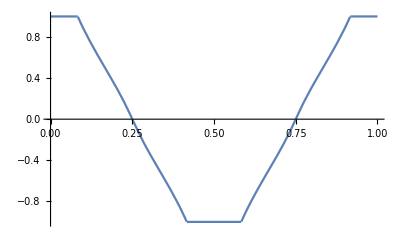

```mathematica
Plot[f[x],{x,0,1}]
```

```mathematica
ff[x_]=f[Mod[Abs[x],1]];
```

```mathematica
s0=N[Log[2]/Log[3]]
```

0.63093

```mathematica
(*Phased  Mandelbrot Cartoon Function*)
```

```mathematica
kk[x_]=N[Sum[ff[3^k*x]/3^(s0*k),{k,0,20}]];
```

```mathematica
ll[x_]=N[Sum[ff[3^k*(x+1/4)]/3^(s0*k),{k,0,20}]];
```

```mathematica
mm[x_]=N[Sum[ff[3^k*(x-1/4)]/3^(s0*k),{k,0,20}]];
```

```mathematica
n0=750000;
pts=Join[Delete[Reverse[Union[ParallelTable[{ll[t],kk[t],mm[t]},{t,0,1,1/n0}]]],1],Delete[Reverse[Union[ParallelTable[{kk[t],ll[t],mm[t]},{t,0,1,1/n0}]]],1],Delete[Reverse[Union[ParallelTable[{ll[t],mm[t],kk[t]},{t,0,1,1/n0}]]],1]];
```

```mathematica
Dimensions[pts]
```

```mathematica
(*6. Voxelization*)
voxel=0.02;

voxels=DeleteDuplicates[Floor[pts/voxel]];
cuboids={Hue[Norm[#]/3],Cuboid[#*voxel,(#+1)*voxel]}&/@voxels;
```

```mathematica
(*7. Render voxel fractal*)
g1=Graphics3D[{Pink,EdgeForm[],cuboids},Boxed->False,Background->Black,ImageSize->{2000,2000}];
```

```mathematica
Export["Biscuit_3xHexagon_3d_750000_voxel_BackBlack_g1.jpg",g1];
```

```mathematica
g2=Show[g1,ViewPoint->Above,ImageSize->{2000,2000}];
```

```mathematica
Export["Biscuit_3xHexagon_3d_750000_voxel_BackBlack_g2.jpg",g2];
```

```mathematica
g3=Show[g1,ViewPoint->Front,ImageSize->{2000,2000}];
```

```mathematica
Export["Biscuit_3xHexagon_3d_750000_voxel_BackBlack_g3.jpg",g3];
```

```mathematica
g4=Show[g1,ViewPoint->{1.,-2,-2},ImageSize->{2000,2000}];
```

```mathematica
Export["Biscuit_3xHexagon_3d_750000_voxel_BackBlack_g4.jpg",g4];
```

```mathematica
Export["Biscuit_3xHexagon_3d_750000_voxel_BackBlack_grid.jpg",Rasterize[GraphicsGrid[{{g1,g2},{g3,g4}}],"Image",ImageSize->4000]]
```

```mathematica
Export["Biscuit_3xHexagon_3d_750000_voxel_.stl",g1]
```

```mathematica
model =Import["Biscuit_3xHexagon_3d_250000_voxel_.stl"]
```

```mathematica
prt=Printout3D[model,"Biscuit_3xHexagon_3d_750000_voxel_stl_PRT.stl"]
```

```mathematica
(*end*)
```